## Expected F_st under the models of divergence with gene flow

### One-way continuous migration, two N_e

```mathematica
varb = ψ[ω,{{{a}},{{b}}},{{x},{y}},Coalescence->λ,Migration->M,Splits->Λ];
varw1= ψ[ω,{{{a},{a}},{}},{{x},{y}},Coalescence->λ,Migration->M,Splits->Λ];
varw2 = ψ[ω,{{},{{b},{b}}},{{x},{y}},Coalescence->λ,Migration->M,Splits->Λ];
```

```mathematica
varrls={M[{x},{y}]->0,M[{y},{x}]->M,Λ[{{x},{y}}]->Λ,λ[{x,y}]->1,λ[{y}]->1};
twoEGF=({MakeSolvedGF[varb,{{{X}},{{Y}}},varrls],MakeSolvedGF[varw1,{{{X},{X}},{}},varrls],MakeSolvedGF[varw2,{{},{{Y},{Y}}},varrls]}/.ω[_]->ω/.λ[{y}]->1/.a1->f)//Flatten
```

{-(-M-2 Λ)/((1+2 ω) (M+2 Λ+4 ω)),-(-M^2-3 M Λ-2 Λ^2-4 Λ ω-M λ[{x}]-2 Λ λ[{x}]-4 ω λ[{x}]-2 M ω λ[{x}]-4 Λ ω λ[{x}]-8 ω^2 λ[{x}])/((1+2 ω) (M+2 Λ+4 ω) (M+Λ+2 ω+λ[{x}])),1/(1+2 ω)}

```mathematica
twoEGFInvrtd=InverseLaplaceTransform[(Λ^-1 twoEGF),Λ,T]//Simplify
```

{(M+4 ⅇ^(-1/2 T (M+4 ω)) ω)/((1+2 ω) (M+4 ω)),-(-8 ⅇ^(-1/2 T (M+4 ω)) M ω (M+2 ω+λ[{x}])-(M+2 λ[{x}]) (M^2+(1+2 ω) (M+4 ω) λ[{x}])+2 ⅇ^(-T (M+2 ω+λ[{x}])) ω (M+4 ω) (M+(-2+M) λ[{x}]+2 λ[{x}]^2))/((1+2 ω) (M+4 ω) (M+2 ω+λ[{x}]) (M+2 λ[{x}])),1/(1+2 ω)}

#### Expected branch lengths and F_st

```mathematica
twoEExpP=-D[twoEGFInvrtd,ω]/.ω->0
```

{2+4/M-(4 ⅇ^(-(M T)/2))/M,(2 (M^2+M λ[{x}]))/(M (M+λ[{x}])^2)+(4 (M^2+M λ[{x}]))/(M^2 (M+λ[{x}]))+(2 (M^2+M λ[{x}]))/(M (M+λ[{x}]))+(-8 ⅇ^(-(M T)/2) M (M+λ[{x}])-(M+2 λ[{x}]) (4 λ[{x}]+2 M λ[{x}])+2 ⅇ^(-T (M+λ[{x}])) M (M+(-2+M) λ[{x}]+2 λ[{x}]^2))/(M (M+λ[{x}]) (M+2 λ[{x}])),2}

```mathematica
twotw=(twoEExpP⟦2⟧+twoEExpP⟦3⟧)/2;twotb=twoEExpP⟦1⟧; twott=(twotw+twotb)/2;twoFst=Simplify[(twott-twotw)/twott]
```

((-1+ⅇ^(T (M+λ[{x}]))) M^2+M (2-8 ⅇ^((M T)/2+T λ[{x}])-M+ⅇ^(T (M+λ[{x}])) (6+M)) λ[{x}]+2 (-4 ⅇ^((M T)/2+T λ[{x}])-M+ⅇ^(T (M+λ[{x}])) (4+M)) λ[{x}]^2)/(M^2 (1-8 ⅇ^((M T)/2+T λ[{x}])+ⅇ^(T (M+λ[{x}])) (7+4 M))+M (-2-16 ⅇ^((M T)/2+T λ[{x}])+M+ⅇ^(T (M+λ[{x}])) (18+11 M)) λ[{x}]+2 (-4 ⅇ^((M T)/2+T λ[{x}])+M+ⅇ^(T (M+λ[{x}])) (4+3 M)) λ[{x}]^2)

```mathematica
currentWinner={theta->1.1304654956345690297`5.,λ[{x}]->2.3494632908288530253`5.,T->1.0451223974006710784`5.,M->3.613226231838105099`5.};
```

```mathematica
expFst=twoFst/.currentWinner
```

0.181

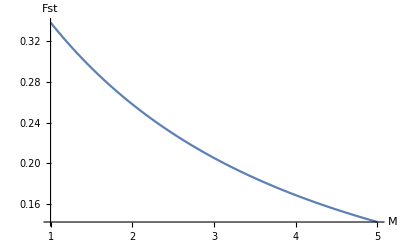

```mathematica
Plot[twoFst/.Drop[currentWinner,-1],{M,1,5},AxesLabel->{"M","Fst"}]
```

### Discrete admixture, two N_e

```mathematica
varAD2b=ψ[ω,{{{a}},{{b}}},{{x},{y}},Admixture->{{Subscript[A, 1],Subscript[a, 1]},{Subscript[A, 2],Subscript[a, 2]}},Coalescence->λ];
varAD2w1=ψ[ω,{{{a},{a}},{}},{{x},{y}},Admixture->{{Subscript[A, 1],Subscript[a, 1]},{Subscript[A, 2],Subscript[a, 2]}},Coalescence->λ];
varAD2w2=ψ[ω,{{},{{b},{b}}},{{x},{y}},Admixture->{{Subscript[A, 1],Subscript[a, 1]},{Subscript[A, 2],Subscript[a, 2]}},Coalescence->λ];
varrlsG={Subscript[A, 1][{x},{y}]->0,Subscript[A, 2][{x},{y}]->0,Subscript[a, 1][{x},{y}]->0,Subscript[a, 2][{x},{y}]->0,Subscript[A, 1][{y},{x}]->A1,Subscript[A, 2][{y},{x}]->A2,Subscript[a, 1][{y},{x}]->a1,Subscript[a, 2][{y},{x}]->1};
```

```mathematica
twoEADGFL={MakeSolvedGF[varAD2b,{{{X}},{{Y}}},varrlsG],MakeSolvedGF[varAD2w1,{{{X},{X}},{}},varrlsG],MakeSolvedGF[varAD2w2,{{},{{Y},{Y}}},varrlsG]}//Flatten
```

{(A1 λ[{y}] (A2+a1 ω[{a}]+a1 ω[{b}]))/((A1+ω[{a}]+ω[{b}]) (A2+ω[{a}]+ω[{b}]) (λ[{y}]+ω[{a}]+ω[{b}])),-((-A1 A2^2 λ[{y}]-A1 A2 λ[{x}] λ[{y}]-A2^2 λ[{x}] λ[{y}]-A2 λ[{x}]^2 λ[{y}]-2 A1 A2 λ[{x}] ω[{a}]+4 a1 A1 A2 λ[{x}] ω[{a}]-2 a1^2 A1 A2 λ[{x}] ω[{a}]-2 A2^2 λ[{x}] ω[{a}]-2 A2 λ[{x}]^2 ω[{a}]-2 A1 A2 λ[{y}] ω[{a}]-2 a1^2 A1 A2 λ[{y}] ω[{a}]-2 A1 λ[{x}] λ[{y}] ω[{a}]+4 a1 A1 λ[{x}] λ[{y}] ω[{a}]-4 a1^2 A1 λ[{x}] λ[{y}] ω[{a}]-4 A2 λ[{x}] λ[{y}] ω[{a}]-2 λ[{x}]^2 λ[{y}] ω[{a}]-4 A1 λ[{x}] ω[{a}]^2+8 a1 A1 λ[{x}] ω[{a}]^2-4 a1^2 A1 λ[{x}] ω[{a}]^2-8 A2 λ[{x}] ω[{a}]^2-4 λ[{x}]^2 ω[{a}]^2-4 a1^2 A1 λ[{y}] ω[{a}]^2-4 λ[{x}] λ[{y}] ω[{a}]^2-8 λ[{x}] ω[{a}]^3)/((A2+2 ω[{a}]) (A1+λ[{x}]+2 ω[{a}]) (A2+λ[{x}]+2 ω[{a}]) (λ[{y}]+2 ω[{a}]))),λ[{y}]/(λ[{y}]+2 ω[{b}])}

```mathematica
twoEADGFLInvrtd=InverseLaplaceTransform[(A1^-1 A2^-1 twoEADGFL),{A1,A2},{T1,T2}]/.ω[_]->ω/.λ[{y}]->1/.a1->f
```

{(ⅇ^(-2 T1 ω) (ⅇ^(-2 T2 ω) (1-f)+f))/(1+2 ω),-(2 ⅇ^(-2 T2 ω-T1 (2 ω+λ[{x}])) (-1+f) f+(2 ⅇ^(-T1 (2 ω+λ[{x}])-T2 (2 ω+λ[{x}])) (-1+f)^2 ω (-1+λ[{x}]))/(2 ω+λ[{x}])-(ⅇ^(-T1 (2 ω+λ[{x}])) (2 f^2 ω+ⅇ^(T1 (2 ω+λ[{x}])) λ[{x}]-2 f λ[{x}]+2 f^2 λ[{x}]+2 ⅇ^(T1 (2 ω+λ[{x}])) ω λ[{x}]-4 f ω λ[{x}]+2 f^2 ω λ[{x}]))/(2 ω+λ[{x}]))/(1+2 ω),1/(1+2 ω)}

#### Expected branch lengths and F_st

```mathematica
twoEADExpP=-D[twoEADGFLInvrtd,ω]/.ω->0/.T2->T-T1
```

{2+2 (1-f) (T-T1)+2 T1,2 ⅇ^(-T1 λ[{x}]) (-1+f) f (-2 (T-T1)-2 T1)+(2 ⅇ^(-(T-T1) λ[{x}]-T1 λ[{x}]) (-1+f)^2 (-1+λ[{x}]))/λ[{x}]+(2 ⅇ^(-T1 λ[{x}]) (ⅇ^(T1 λ[{x}]) λ[{x}]-2 f λ[{x}]+2 f^2 λ[{x}]))/λ[{x}]^2+(2 ⅇ^(-T1 λ[{x}]) T1 (ⅇ^(T1 λ[{x}]) λ[{x}]-2 f λ[{x}]+2 f^2 λ[{x}]))/λ[{x}]-(ⅇ^(-T1 λ[{x}]) (2 f^2+2 ⅇ^(T1 λ[{x}]) λ[{x}]-4 f λ[{x}]+2 f^2 λ[{x}]+2 ⅇ^(T1 λ[{x}]) T1 λ[{x}]))/λ[{x}]-2 (2 ⅇ^(-T1 λ[{x}]) (-1+f) f-(ⅇ^(-T1 λ[{x}]) (ⅇ^(T1 λ[{x}]) λ[{x}]-2 f λ[{x}]+2 f^2 λ[{x}]))/λ[{x}]),2}

```mathematica
twoADtw=(twoEADExpP⟦2⟧+twoEADExpP⟦3⟧)/2;twoADtb=twoEADExpP⟦1⟧; twoADtt=(twoADtw+twoADtb)/2; twoADFst=Simplify[(twoADtt-twoADtw)/twoADtt]
```

(ⅇ^(T λ[{x}])-(-1+f)^2+ⅇ^((T-T1) λ[{x}]) (-2+f) f+((-1+f)^2+ⅇ^(T λ[{x}]) (-1+2 (-1+f) T-2 f T1)-ⅇ^((T-T1) λ[{x}]) f (-2+f-2 T+2 f T+2 T1-2 f T1)) λ[{x}])/(-ⅇ^(T λ[{x}])+(-1+f)^2-ⅇ^((T-T1) λ[{x}]) (-2+f) f+(-(-1+f)^2+ⅇ^(T λ[{x}]) (-3+2 (-1+f) T-2 f T1)+ⅇ^((T-T1) λ[{x}]) f (-2+f-2 T+2 f T+2 T1-2 f T1)) λ[{x}])

```mathematica
twoADFst/.currentWinner
```

(11.65-(-1+f)^2+ⅇ^(2.3495 (1.0451-T1)) (-2+f) f+2.3495 ((-1+f)^2+11.65 (-1+2.0902 (-1+f)-2 f T1)-ⅇ^(2.3495 (1.0451-T1)) f (-4.0902+3.0902 f+2 T1-2 f T1)))/(-11.65+(-1+f)^2-ⅇ^(2.3495 (1.0451-T1)) (-2+f) f+2.3495 (-(-1+f)^2+11.65 (-3+2.0902 (-1+f)-2 f T1)+ⅇ^(2.3495 (1.0451-T1)) f (-4.0902+3.0902 f+2 T1-2 f T1)))

```mathematica
4.8580*0.01*currentWinner⟦3,2⟧
```

0.050772

```mathematica
Solve[(twoADFst/.currentWinner/.T1->0.01)==expFst,{f} ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{f→0.38906},{f→1.37908}}

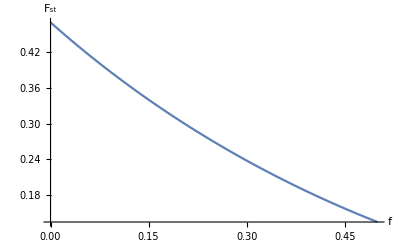

```mathematica
Plot[twoADFst/.best/.T1->0.02,{f,0,0.5}, AxesLabel->{"f","F_st"}]
```

The expectation of F_stunder the  IM and the admixture model converges to the same expression in the absence of gene flow as it should!

```mathematica
{twoADFst/.f->0,Limit[twoFst,M->0]}
```

{(-1+ⅇ^(T λ[{x}])+(1+ⅇ^(T λ[{x}]) (-1-2 T)) λ[{x}])/(1-ⅇ^(T λ[{x}])+(-1+ⅇ^(T λ[{x}]) (-3-2 T)) λ[{x}]),(1-ⅇ^(T λ[{x}])+(-1+ⅇ^(T λ[{x}]) (1+2 T)) λ[{x}])/(-1+ⅇ^(T λ[{x}])+(1+ⅇ^(T λ[{x}]) (3+2 T)) λ[{x}])}

```mathematica
{twoADFst/.f->0,Limit[twoFst,M->0]}/.currentWinner
```

{0.47,0.47}